# Disease invasion is facilitated by landscape heterogeneity

## This notebook contains the code to perform the analysis investigating the effect of various forms of landscape heterogeneity on the invasion of a disease in a landscape

## Some set up

```mathematica
(*First, some directory stuff for outputting plot*)
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir=FileNameJoin[{baseDir,"figs"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}];

(*Define constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;
```

## Background for the model

We are considering a model where the probability of an individual organism at baseline existing in a given cell  is given by  where . The values of T and S are drawn from two normal distributions . For the purposes of calculation and visualization, we can extend this to a two-dimensional space, such that  become

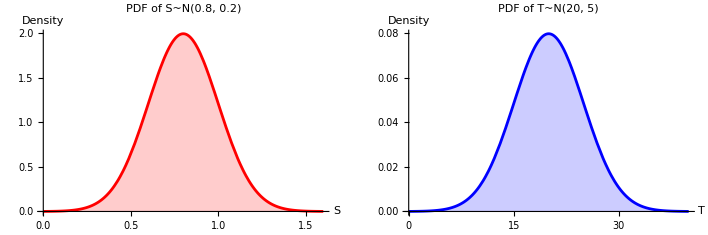

```mathematica
(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*adjust for larger or smaller landscapes*)

(*Generate random values for T and S across the grid*)
meanT = 20;
varT = 5;
meanS = 0.8;
varS = 0.2 ;
Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[NormalDistribution[meanS,varS],gridSize];

(*Plot as a density plot*)
pdfPlotS=Plot[PDF[NormalDistribution[meanS,varS],x],{x,meanS - 4*varS,(meanS + 4*varS)},
	PlotLabel->Style[Text@StringJoin["PDF of S~N(",ToString[meanS],", ",ToString[varS],")"],14],
	Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},
	PlotLabel->Style[Text@StringJoin["PDF of T~N(",ToString[meanT],", ",ToString[varT],")"],14],
	Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
	
(*Display the pdfs*)
SandTPDFS = GraphicsGrid[{{Style[pdfPlotS, FontSize->Scaled[0.04]],Style[pdfPlotT, FontSize->4]}}];
Show[SandTPDFS, ImageSize->6/2.54*300]
Export[relativePath["figs","temp-supply-wij-pdfs.pdf"],
	SandTPDFS, ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

## Standard landscape probabilities

We calculate the landscape probabilities and truncate them to be greater than zero, and if we consider a 2D space, we can plot all the options together.

```mathematica
(*Compute probabilities w_{i,j} across the landscape*)
(*Truncate landscape probabilities to be>=0*)
landscapeProbabilities=Table[Max[0,w[Tgrid[[i,j]],Sgrid[[i,j]]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];

(*Heatmap for w_{i,j} values with Magma color scheme*)
heatmapW=ArrayPlot[landscapeProbabilities,
	ColorFunction->"Pastel",Mesh->False,
	PlotLabel->"Probability Landscape ( ≥ 0)",
	PlotLegends->Automatic];

(*Heatmap for T values with TemperatureMap color scheme*)
heatmapT=ArrayPlot[Tgrid,ColorFunction->"TemperatureMap",Mesh->False,
	PlotLabel->"Temperature (T) Landscape",PlotLegends->Automatic];

(*Heatmap for S values with purple gradient color scheme*)
heatmapS=ArrayPlot[Sgrid,ColorFunction->(Blend[{White,Purple},#]&),
	Mesh->False,PlotLabel->"Supply (S) Landscape",PlotLegends->Automatic];

(*Arrange the plots in a grid with T and S on the top row,w at double size on the second row*)
threeArray = GraphicsGrid[{{Style[heatmapT, 
	FontSize->Scaled[0.04]],Style[heatmapS, FontSize->4],
	Style[heatmapW, FontSize->4]}},Spacings->{2,1}];
Show[threeArray, ImageSize->6/2.54*300]
Export[relativePath["figs","temp-supply-probability-landscape.pdf"],threeArray, 
	ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

-Graphics-

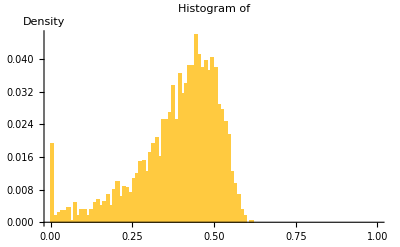

```mathematica
(*Flatten the landscape probabilities for density plot*)
flatProbabilities=Flatten[landscapeProbabilities];
hist=Histogram[flatProbabilities,{0, 1, 0.01},"Probability",
	PlotLabel->Style[Text@StringJoin["Histogram of "],14],
	AxesLabel->{"","Density"}];
hist
```

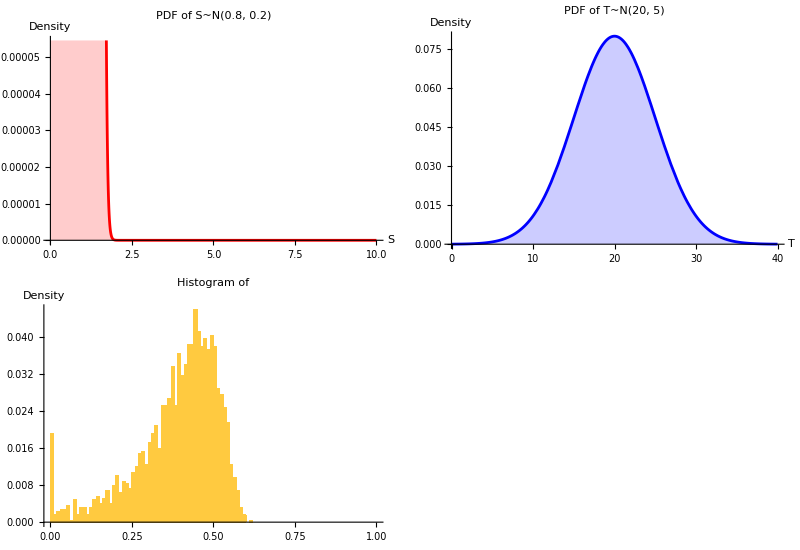

```mathematica
(*Display all three plots*)
GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist}},Spacings->{2,1}]
```

## Now, from the values, calculate the normalized co-occurrence probabilities.

So now, we want to state that each normalized probability is:

```mathematica
(*Step 1:Calculate normalized probabilities x_{i,j}*)
totalSum=Total[Total[landscapeProbabilities]];
normalizedProbabilities=landscapeProbabilities/totalSum;

(*Step 2:Calculate normalized co-occurrence probabilities *)
normalizedCoOccurrence=normalizedProbabilities^2;

(*Step 3:Plot normalized co-occurrence probabilities with a blue-to-red gradient*)
coOccurrenceHeatmap=ArrayPlot[normalizedCoOccurrence,ColorFunction->(Blend[{Blue,Red},#]&),
	Mesh->True,PlotLabel->"Normalized Co-Occurrence Probability Landscape ",PlotLegends->Automatic];

(*Display the heatmap*)
coOccurrenceHeatmap = GraphicsGrid[{{Style[coOccurrenceHeatmap, FontSize->Scaled[0.04]]}}];
coOccurrenceHeatmap
Export[relativePath["figs","cooccurence-heatmaps.pdf"],coOccurrenceHeatmap, 
ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

-Graphics-

## Simulate from the probability function

```mathematica
(* Define constants *)
R0 = 0.5;  (* Half-saturation constant for resource uptake *)
ma = 0.01; mb = 0.1; mc = 0.05; (* Metabolic rate parameters *)
TI = 20;  (* Optimal temperature *)
γ = 150;  (* Temperature response breadth *)

(* Define functions for Imax and m *)
Imax[T_] := Exp[-((T - TI)^2)/γ];  (* Maximum intake rate as a function of T *)
m[T_] := ma Exp[mb T] + mc;  (* Metabolic rate function *)

(* Define probability function w[T, R] *)
w[T_, R_] := Max[0, (Imax[T] * R) / (R + R0) - m[T]];

(* Function to compute normalized w[T, R] across a 1D space *)
normalizedW[n_, meanT_, varT_, meanR_, varR_] := Module[
  {Tgrid, Rgrid, Wgrid, totalW},
  
  (* Generate random values for T and S from normal distributions *)
  Tgrid = RandomVariate[NormalDistribution[meanT, varT], n];
  Rgrid = RandomVariate[NormalDistribution[meanR, varR], n];
  
  (* Compute w[T, S] for each location in the 1D space *)
  Wgrid = MapThread[w, {Tgrid, Rgrid}];
  
  (* Normalize Wgrid to ensure probabilities sum to 1 *)
  totalW = Total[Wgrid];
  Wgrid / totalW
];
(* Define the epsilon function for transmission probability *)
epsilon = 1; (* Assume a constant transmission probability for now *)

(* Compute the probability of disease spreading in a location, φ_i(k, I=1) *)
PhiI[S_, w_] := epsilon * w *(1 - (1 - w)^S)

(* Define simulation parameters *)
n = 100;  (* Number of spatial locations *)
meanT = 20; varT = 5;  (* Parameters for T distribution *)
meanR = 0.8; varR = 0.2;  (* Parameters for R distribution *)

(* Generate normalized suitability probabilities *)
Wgrid = normalizedW[n, meanT, varT, meanR, varR];
(*Print["the sum of Wgrid is ", Total[Wgrid]]*)

(* Compute the ϕ(i) values for the entire 1D space assuming S = 2 *)
S = 1;
PhiGrid = Table[PhiI[S, Wgrid[[i]]], {i, n}];

(* Reshape PhiGrid into a square grid for visualization *)
sqrtN = Sqrt[n];
If[IntegerQ[sqrtN], 
  PhiMatrix = Partition[PhiGrid, sqrtN];
  landscapeProb = ArrayPlot[PhiMatrix, ColorFunction -> "TemperatureMap", 
    PlotLabel -> Style["Disease Spread Probability Grid φ", FontSize -> 12],
    FrameLabel -> {Style["Grid Y", FontSize -> 10], Style["Grid X", FontSize -> 10]}, 
    PlotLegends -> Automatic];
    
    (*So we can see the plots of the two values of R and T together, let's plot 
    those in grids as well*)
    Tmatrix = ArrayReshape[Tgrid, sqrtN];
    Rmatrix = ArrayReshape[Rgrid, sqrtN];
	(*Heatmap for T values with TemperatureMap color scheme*)
	heatmapT=ArrayPlot[Tmatrix,ColorFunction->"TemperatureMap",Mesh->False,
		PlotLabel->"Temperature (T) Landscape",PlotLegends->Automatic];
	
	(*Heatmap for S values with purple gradient color scheme*)
	heatmapR=ArrayPlot[Partition[Rgrid, sqrtN],ColorFunction->(Blend[{White,Purple},#]&),
		Mesh->False,PlotLabel->"Supply (S) Landscape",PlotLegends->Automatic];
	
	(*Arrange the plots in a grid with T and S on the top row,w at double size on the second row*)
	threeArray = GraphicsGrid[{{Style[heatmapT, 
		FontSize->Scaled[0.04]],Style[heatmapR, FontSize->4],
		Style[heatmapW, FontSize->4]}},Spacings->{2,1}];
	Show[threeArray, ImageSize->6/2.54*300]
(*	Export[relativePath["figs","temp-supply-probability-landscape.pdf"],threeArray, 
		ImageSize -> 6/2.54*300, ImageResolution -> 1200];*)

  (* Export the grid plot *)
  Export["disease_spread_grid.pdf", landscapeProb, ImageSize -> 300, ImageResolution -> 1200],
  
  Print["Warning: n is not a perfect square. Cannot reshape into a square grid."]
];
(*landscapeProb*)

(* Plot histogram of w_i values *)
wHistogram = Histogram[Wgrid, Automatic, "PDF", 
	PlotLabel->Style[Text@StringJoin["Histogram of "],14],
	AxesLabel->{"","Density"}]

(* Plot probability distribution function of T *)
pdfPlotR=Plot[PDF[NormalDistribution[meanR,varR],x],{x,meanR - 4*varR,(meanR + 4*varR)},
	PlotLabel->Style[Text@StringJoin["PDF of R~N(",ToString[meanR],", ",ToString[varR],")"],14],
	Filling->Axis,PlotStyle->Red,AxesLabel->{"R","Density"},ImageSize->Medium]
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},
	PlotLabel->Style[Text@StringJoin["PDF of T~N(",ToString[meanT],", ",ToString[varT],")"],14],
	Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium]

(* Export plots *)
Export["w_histogram.pdf", wHistogram, ImageSize -> 300, ImageResolution -> 1200];
Export["pdf_T.pdf", pdfPlotT, ImageSize -> 300, ImageResolution -> 1200];
Export["pdf_R.pdf", pdfPlotR, ImageSize -> 300, ImageResolution -> 1200];

(* Plot the probability of disease spread along the 1D space *)
landscapeHist = Histogram[PhiGrid, Automatic, "PDF",
  PlotLabel -> Style["Probability Distribution of Disease Spread", FontSize -> 12],
  AxesLabel -> {Style["Probability", FontSize -> 10], Style["Density", FontSize -> 10]}];
landscapeHist
(* Export the plot *)
Export["disease_spread_1d.pdf", landscapeProb, ImageSize -> 300, ImageResolution -> 1200];

(* Calculate the overall probability of disease spread *)
Total[PhiGrid]

(* Print the result *)
(*BoldPhi*)
```

Rgrid